```mathematica
mm=10;
pcc=GraphData[{"Planar","Cubic","Connected"},;;mm]
pcb=GraphData[{"Planar","Cubic","Connected","Bicolorable"},;;mm]
```

{{Cubic,{8,2}},{Cubic,{10,1}},{Cubic,{10,2}},{Cubic,{10,3}},{Cubic,{10,4}},{Cubic,{10,6}},{Cubic,{10,7}},{Cubic,{10,11}},{Cubic,{10,12}},CubicalGraph,{Matchstick,3},{Prism,3},{Prism,5},TetrahedralGraph}

{CubicalGraph}

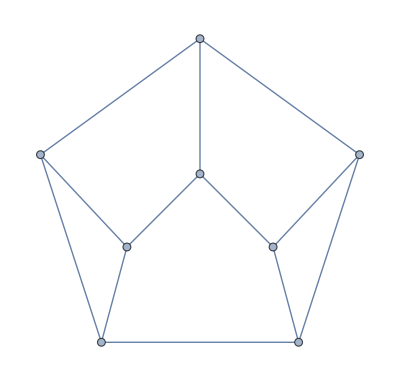
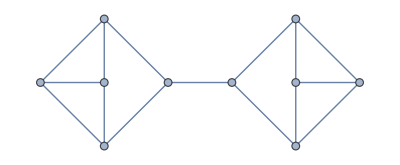
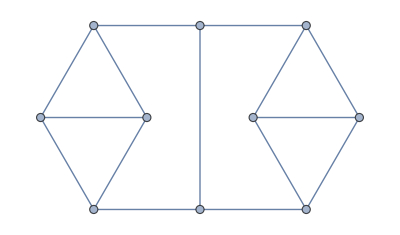
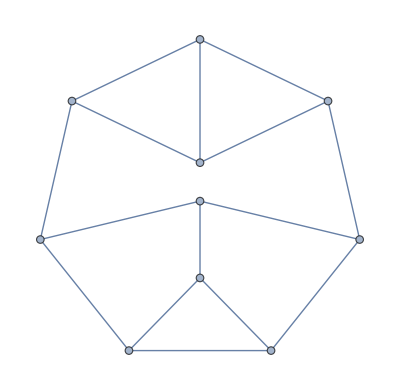
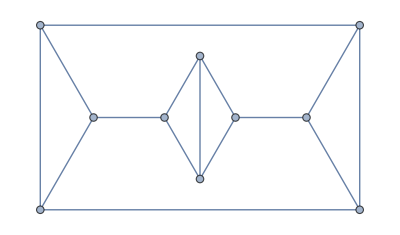
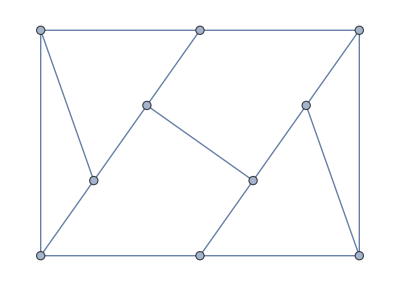
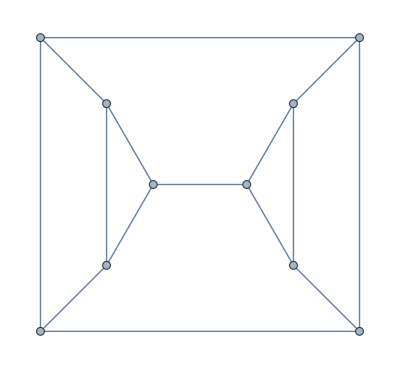
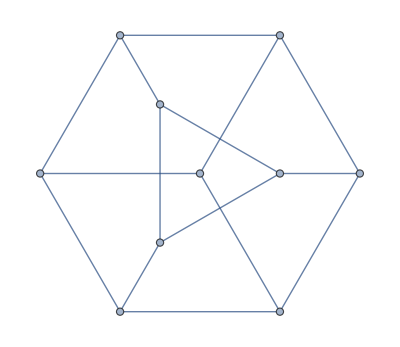

```mathematica
Map[GraphData,pcc]
```

```mathematica
t1=GraphData[{"Prism",3}]
```

-Graphics-

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Map[ChromaticNumber,Map[FromAdjacencyMatrix[Normal[AdjacencyMatrix[GraphData[#]]]]&,pcc]]
```

{3,3,3,3,3,3,3,3,3,2,3,3,3,4}

```mathematica
list2cycle[list_]:=Flatten[Table[Table[list[[i]]<->list[[j]],{i,1,j-1}],{j,2,Length[list]}]]
list2cycle[{1,2}]
list2cycle[{1,2,3}]
```

{1<->2}

{1<->2,1<->3,2<->3}

```mathematica
Length[l[[2]]]
```

```mathematica
l2edges[l_]:=Join[Map[l[[1]]<->#&,l[[2]]],list2cycle[l[[2]]]]
l2edges[{2,{1,4}}]
l2edges[{2,{1,4,5}}]
```

{2<->1,2<->4,1<->4}

{2<->1,2<->4,2<->5,1<->4,1<->5,4<->5}

```mathematica
ordedge[e_]:=Block[{s=Sort[{e[[1]],e[[2]]}]},(s[[1]])<->(s[[2]])]
Map[ordedge,{5<->3,2<->3,2<->5}]
```

{3<->5,2<->3,2<->5}

```mathematica
t2=HypercubeGraph[2];
```

{1,2,3,4}

{1<->2,1<->3,2<->4,3<->4}

{{1,{2,3}},{2,{1,4}},{3,{1,4}},{4,{2,3}}}

{{1<->2,1<->3,2<->3},{2<->1,2<->4,1<->4},{3<->1,3<->4,1<->4},{4<->2,4<->3,2<->3}}

{1<->2,1<->3,2<->3,2<->1,2<->4,1<->4,3<->1,3<->4,1<->4,4<->2,4<->3,2<->3}

{1<->2,1<->3,2<->3,2<->4,1<->4,3<->4}

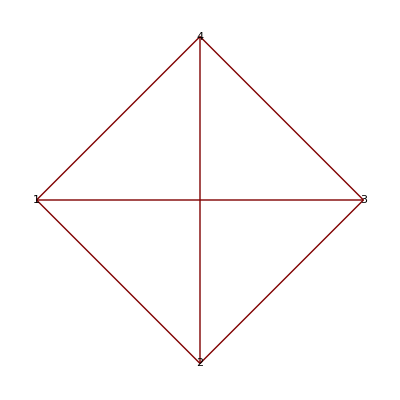

```mathematica
g=t2;
GraphPlot[g,VertexLabeling->True];
vlist=VertexList[g]
elist=EdgeList[g]
Map[{#,Complement[VertexList[NeighborhoodGraph[g,#]],{#}]}&,vlist]
Map[l2edges,%]
Flatten[%]
DeleteDuplicates[Map[ordedge,%]]
GraphPlot[Graph[%],VertexLabeling->True]
```

```mathematica
"I need to modify this to make new vertices, this is overlapping them."
```

```mathematica
makeclusters[list_]:=Block[{vertexnum=0,outlist={},listpos=1,thislist={},thisrange={},thiscycle={}},
For[listpos=1,listpos≤Length[list],listpos++,
thislist=list[[listpos]];
thisrange=Range[vertexnum+1,vertexnum+Length[thislist[[2]]]];
thiscycle=list2cycle[thisrange];
AppendTo[outlist,{vertexnum+1,thiscycle,thisrange,thislist[[2]]}];
vertexnum=vertexnum+Length[thislist[[2]]];
];
outlist
]
makeclusters[{{1,{2,3}},{2,{1,4}},{3,{1,4}},{4,{2,3}}}]
```

{{1,{1<->2},{1,2},{2,3}},{3,{3<->4},{3,4},{1,4}},{5,{5<->6},{5,6},{1,4}},{7,{7<->8},{7,8},{2,3}}}

```mathematica
EdgeList[t2]
```

{1<->2,1<->3,2<->4,3<->4}

```mathematica
GraphPlot[g,VertexLabeling->True];
vlist=VertexList[g]
elist=EdgeList[g]
Map[{#,Complement[VertexList[NeighborhoodGraph[g,#]],{#}]}&,vlist]
Map[l2edges,%]
clusters=makeclusters[%]
sofar=Map[#[[2]]&,clusters]
clusters=Map[#[[3]]&,clusters]
Block[{i=1,outlist={},thisx=0,thisy=0,newx=0,newy=0,localclusters=clusters},For[i=1,i<Length[elist],i++,
thisx=elist[[i,1]];
thisy=elist[[i,2]];
Print[{thisx,thisy}];
newx=localclusters[[thisx]][[1]];
newy=localclusters[[thisy]][[1]];
AppendTo[outlist,newx<->newy];
localclusters=Delete[localclusters,{newx,1}];
localclusters=Delete[localclusters,{newy,1}];
];
{outlist,localclusters}]
```

{1,2,3,4}

{1<->2,1<->3,2<->4,3<->4}

{{1,{2,3}},{2,{1,4}},{3,{1,4}},{4,{2,3}}}

{{1<->2,1<->3,2<->3},{2<->1,2<->4,1<->4},{3<->1,3<->4,1<->4},{4<->2,4<->3,2<->3}}

{{1,{1<->2},{1,2},1<->3},{3,{3<->4},{3,4},2<->4},{5,{5<->6},{5,6},3<->4},{7,{7<->8},{7,8},4<->3}}

{{1<->2},{3<->4},{5<->6},{7<->8}}

{{1,2},{3,4},{5,6},{7,8}}

{1,2}

{1,3}

Delete::partw: Part {6, 1} of {{2}, {4}, {6}, {7, 8}} does not exist.

{2,4}

Part::partw: Part 4 of Delete[{{2}, {4}, {6}, {7, 8}}, {6, 1}] does not exist.

Delete::partw: Part {6, 1} of Delete[{{2}, {4}, {6}, {7, 8}}, {6, 1}] does not exist.

Delete::psl: Position specification Delete[{{2}, {4}, {6}, {7, 8}}, {6, 1}] in Delete[Delete[{{2}, {4}, {6}, {7, 8}}, {6, 1}], {6, 1}] is not a machine-sized integer or a list of machine-sized integers.

{{1<->3,2<->6,6<->Delete[{{2},{4},{6},{7,8}},{6,1}]},Delete[Delete[Delete[{{2},{4},{6},{7,8}},{6,1}],{6,1}],{Delete[{{2},{4},{6},{7,8}},{6,1}],1}]}

```mathematica
"
for each edge in the original graph, 
	get the lists from outlist according to the vertices
	connect the first relevant pair
	delete that pair from the lists
"
```

```mathematica
"
get the nth elem of thisrange = a
connect to the nth elem of outlist-thislist[[a]]
"
```

```mathematica
b={1,2,3}
Delete[b,2]
b
```

{1,2,3}

{1,3}

{1,2,3}